# Homework 5

## Eric Nguyen

```mathematica
ClearAll["Global`*"];
```

### Problem 1

```mathematica
ω0=2π
```

```mathematica
eq1=x''[t]+2*β*x'[t]+(ω0^2)*x[t]==0
```

4 π^2 x[t]+2 β x'[t]+x''[t]==0

#### Part (a) Under damped

```mathematica
sol1a=DSolve[{eq1/.{β->0.05ω0},x[0]==5,x'[0]==2ω0},x[t],t]//Simplify
```

{{x[t]→ⅇ^(-0.314159 t) (5. Cos[6.27533 t]+2.25282 Sin[6.27533 t])}}

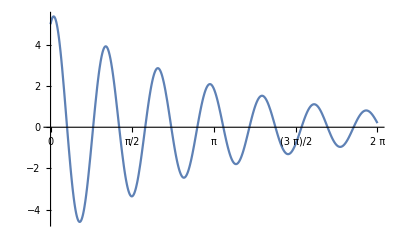

```mathematica
plot1a=Plot[x[t]/.sol1a[[1]],{t,0,2π},Ticks->{Range[0,2π,π/4], Automatic}]
```

#### Part (b) Over damped

```mathematica
sol1b=DSolve[{eq1/.{β->1.5ω0},x[0]==1,x'[0]==-2ω0},x[t],t]//Simplify
```

{{x[t]→0.723607 ⅇ^(-16.4496 t)+0.276393 ⅇ^(-2.39996 t)}}

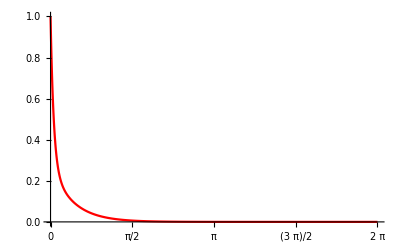

```mathematica
plot1b=Plot[x[t]/.sol1b[[1]],{t,0,2π},PlotStyle->Red,Ticks->{Range[0,2π,π/4], Automatic},PlotRange->{0,1}]
```

#### Part (c) Critically damped

```mathematica
sol1c=DSolve[{eq1/.{β->ω0},x[0]==1,x'[0]==-2ω0},x[t],t]//Simplify
```

{{x[t]→ⅇ^(-2 π t) (1-2 π t)}}

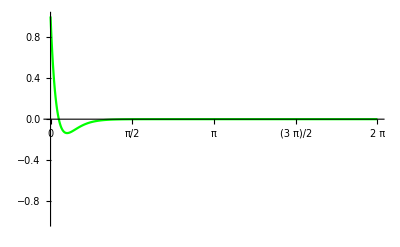

```mathematica
plot1c=Plot[x[t]/.sol1c[[1]],{t,0,2π},PlotStyle->Green,Ticks->{Range[0,2π,π/4], Automatic},PlotRange->{-1,1}]
```

#### Plot each on the same graph

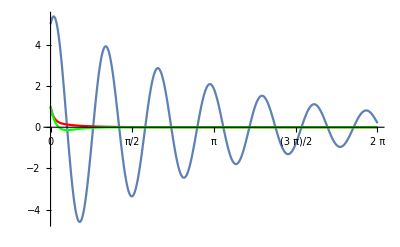

```mathematica
Show[plot1a,plot1b,plot1c]
```

### Problem 2

```mathematica
eq2=x''[t]+2β*x'[t]+ω0^2*x[t]==γ*Cos[ω*t];
```

```mathematica
sol2=DSolve[{eq2,x[0]==0,x'[0]==0},x[t],t];
```

#### Plot for

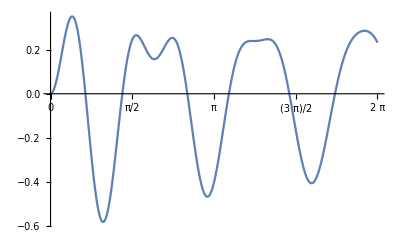

```mathematica
plot2a=Plot[(x[t]/.sol2[[1]])/.{β->0.05ω0,γ->10,ω->0.5ω0},{t,0,2π},Ticks->{Range[0,2π,π/2], Automatic}]
```

#### Plot for

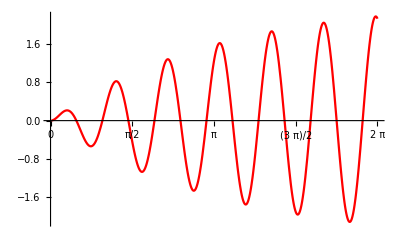

```mathematica
plot2b=Plot[(x[t]/.sol2[[1]])/.{β->0.05ω0,γ->10,ω->ω0},{t,0,2π},PlotStyle->Red,Ticks->{Range[0,2π,π/2], Automatic}]
```

#### Plot for

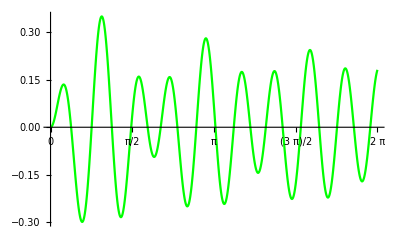

```mathematica
plot2c=Plot[(x[t]/.sol2[[1]])/.{β->0.05ω0,γ->10,ω->1.5ω0},{t,0,2π},PlotStyle->Green,Ticks->{Range[0,2π,π/2], Automatic}]
```

#### Plot each on the same graph

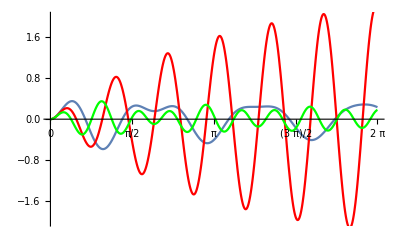

```mathematica
Show[plot2a,plot2b,plot2c,PlotRange->{-2,2},Ticks->{Range[0,2π,π/2], Automatic}]
```

### Problem 3

Using , if  then we make the approximation that . That is, the over damped solution becomes a critically damped solution.

### Problem 4

We want to use the series approach to find solutions for . Write  as .

Use a dummy index .

Rewrite  as .

Combine both series.

For this equation to be valid for all , we require

Plugging in values for the recursion relation we get

The pattern reveals that

Thus the solution for  is

Expanding the series in the solution we get

Notice that the expansions match the series expansion for  and , respectively.

### Problem 5

We want to use the series approach to find solutions for . Write  as

Use a dummy index  and .

Rewrite  as  and  as .

Pull out the first term in the series on the left hand side.

Combine both series.

For this equation to be valid for all , we require

Plugging in values for the recursion relation we get

The pattern reveals that

Thus the solution for  is

Notice there is no term in the series proportional to  and the recursion relations relate every third term of the expansion.

Plot for

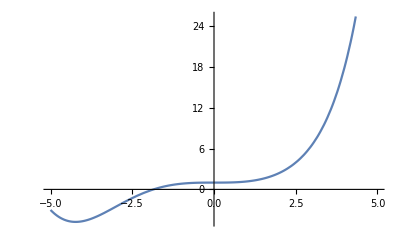

```mathematica
Plot[Sum[x^(3n)/Factorial[3n],{n,0,10}],{x,-5,5}]
```

Plot for

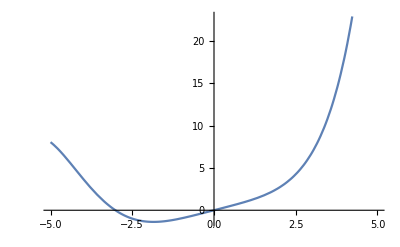

```mathematica
Plot[Sum[x^(3n+1)/Factorial[3n+1],{n,0,10}],{x,-5,5}]
```